# PerturbedCellularAutomaton

Evolve a cellular automaton with changes to certain cells

## Definition

```mathematica
nonzeroRange[list_]:= SparseArray[list]["NonzeroPositions"] // If[Length[#] == 0, #, {#[[1, 1]], #[[-1, 1]]}]&
```

```mathematica
tofunc[bitfuncspec_, k_] := Which[
IntegerQ[bitfuncspec], bitfuncspec&,
bitfuncspec ==="Random", (RandomChoice[Delete[Range[0, k - 1], #+1]]&),
bitfuncspec[[1]] ==="AddValue", (Mod[(# + bitfuncspec[[2]]), k] &),
True, (bitfuncspec[#, k]&)]
```

```mathematica
interprettspec[tspec_]:= Replace[tspec, {
t_Integer:> {t, All},
{t_Integer}:> {t, {t}},
{{t_Integer}}:> {t, t},
{t1_Integer, t2_Integer}:> {t2, t1;;t2},
{t1_Integer, t2_Integer, dt_Integer}:> {t2, t1;;t2;;dt}
}]
```

```mathematica
interpretxspec[xspec___]:= If[xspec === Nothing xspec === Automatic || xspec === All, {-25, 25}, xspec]
```

```mathematica
interprettxspec[txspec_]:= Replace[txspec,{ 
t_Integer :> Append[interprettspec[t], {-25, 25}],
{ts_, xs___}:> Append[interprettspec[ts], interpretxspec[xs]]}]
```

```mathematica
interpretrule[rule_] := Replace[rule, {
   n_Integer :> {n, 2, 1},
   List[n_Integer, k_Integer] :>  {n, k, 1},
   List[n_Integer, k_Integer, r_?NumberQ] :> {n, k, r},
   List[n_Integer, k_Integer, r_?NumberQ, s_Integer] :> {n, k, r},
   List[n_Integer, List[k_Integer, 1]] :> {n, k, 1},
   List[n_Integer, List[k_Integer, 1], r_?NumberQ] :> {n, k, r}
   }]
```

```mathematica
expandrange[idxspec_, t_, start_:1]:= If[t == 0 && start == 1, {}, Replace[idxspec,{
i_Integer:> {i},
{is__} :> {is},
Span[s_, e_] :> Range[s, If[e === All, t, e]], 
f_:> (If[IntegerQ[#], {#}, #]&)[f[Range[start, t]]]
}]]
```

```mathematica
TestCALifeTime[ca_List]:= If[#==0, -Infinity, Length[ca]-#]&[LengthWhile[Reverse[ca],Total[#]==0&]]
```

```mathematica
tosingle[{is_, j_}->r_]:= {#, j}->r&/@is
```

```mathematica
tofullform[idxspec_, t_] := 
 Composition[
   Catenate[tosingle/@#]&,
   MapAt[expandrange[#, t, 0] &, #, Table[{i, 1, 1}, {i, Length[#]}]] &,
   If[! MatchQ[#, _Rule], # -> "Random", #] & /@ # &, 
   Replace[#, Rule[idxs_, val_] :> (# -> val & /@ idxs)] &,
   Replace[#, {
      {ispec_, jspec_} /; (!ListQ[ispec]&&!MatchQ[ispec, _Rule]) :> {{ispec, jspec}},
      Rule[{ispec_, jspec_}, b_] /; (! ListQ[ispec]) :> ({{ispec, jspec} -> b})
      }] &][idxspec]
```

```mathematica
Options[PerturbedCellularAutomaton] = {"ReturnPerturbations"->True, "Body"->False};
```

```mathematica
PerturbedCellularAutomaton[ru_, init_, txspec_, <||>, OptionsPattern[PerturbedCellularAutomaton]]:= 
With[{ca = CellularAutomaton[ru, init, txspec]}, If[OptionValue["ReturnPerturbations"], {ca, <||>}, ca]]
PerturbedCellularAutomaton[ru_, init_, txspec_, {}, OptionsPattern[PerturbedCellularAutomaton]]:= 
With[{ca = CellularAutomaton[ru, init, txspec]}, If[OptionValue["ReturnPerturbations"], {ca, <||>}, ca]]
PerturbedCellularAutomaton[ru_, init_, txspec_, ops:OptionsPattern[PerturbedCellularAutomaton]]:= 
  PerturbedCellularAutomaton[ru, init, txspec, 1, ops]
PerturbedCellularAutomaton[ru_, init_, txspec_, idxspec_Integer, ops:OptionsPattern[]]:= 
  PerturbedCellularAutomaton[ru, init, txspec, {{RandomChoice[#, idxspec] &, RandomChoice}}, 
  Sequence@@Normal[Merge[{{"Body"->True}, ops}, Last]]]
PerturbedCellularAutomaton[ru_, init_, txspec_, idxspec_Integer->b_, ops:OptionsPattern[]]:= 
  PerturbedCellularAutomaton[ru, init, txspec, {{RandomChoice[#, idxspec] &, RandomChoice} -> b}, 
  Sequence@@Normal[Merge[{{"Body"->True}, ops}, Last]]]
```

```mathematica
PerturbedCellularAutomaton[ru_,init_:{{1}, 0}, txspec_:{10, {-25, 25}}, idxspec_:1, OptionsPattern[PerturbedCellularAutomaton]]:= 
Module[{ca, k, tmax, trange, xspec, tpert, fullidxs, pre, ts, indexfunc, evoca, row, rowidxs, rowinrange, expanded, replaced, caperts, pca},
k = interpretrule[ru][[2]];
{tmax, trange, xspec} = interprettxspec[txspec];
 tpert = If[OptionValue["Body"],ca = CellularAutomaton[ru, init, {tmax, xspec}]; If[# == -Infinity, Length[ca]-1, #]&[TestCALifeTime[ca]-1], 
 tmax];
fullidxs = SortBy[tofullform[Normal[idxspec], tpert], #[[1, 1]]&];
pre = If[OptionValue["Body"], ca[[;;fullidxs[[1, 1, 1]]+1]],CellularAutomaton[ru, init,{fullidxs[[1, 1, 1]], xspec}]];
ts = Differences[Append[fullidxs[[All, 1, 1]],  tmax + 1]];
indexfunc = If[OptionValue["Body"],If[# == {}, {}, Range@@#]&[nonzeroRange[#]]&, Range[Length[#]]&];
evoca[{preca_, prepert_}, {{i1_, j1_}->bitfunc_,tcurr_}]:=Module[{},
row = Last[preca];
rowidxs = indexfunc[row];expanded = Select[expandrange[j1, Length[rowidxs]], #<= Length[rowidxs]&];
rowinrange = rowidxs[[expanded]];
{CellularAutomaton[ru, replaced = ReplacePart[row,#->tofunc[bitfunc, k][row[[#]]]&/@rowinrange],tcurr],
Thread[Thread[{i1,rowinrange}]-> replaced[[rowinrange]]]}];
caperts = FoldList[evoca, {pre, {}},Transpose[{fullidxs, ts}]];
pca = Join@@(Most/@caperts[[All, 1]]);
If[OptionValue["ReturnPerturbations"],{pca[[trange]],  Association[Cases[caperts[[2;;, 2]], _Rule, 2]]},
 pca[[trange]]]]
```

## Documentation

### Usage

PerturbedCellularAutomaton[rule,init,txspec]

finds one random location within the body of the automaton and flips the color randomly.

PerturbedCellularAutomaton[rule,init,txspec,n]

finds n random locations within the body of the automaton and flips the color randomly.

PerturbedCellularAutomaton[rule,init,txspec,{tpert,xpert}]

flips the cell specified by {tpert, xpert} to a random bit within the number of colors.

PerturbedCellularAutomaton[rule,init,txspec,{{tpert_1,xpert_1}...}]

flips all cells in the list of perturbations specifications to a random bit within the number of colors.

PerturbedCellularAutomaton[rule,init,txspec,{tpert,xpert}->newbit]

flips the cell at indexes specified by  {tpert, xpert} to the bit specified by newbit.

PerturbedCellularAutomaton[rule,init,txspec,{{tpert_1,xpert_1}->newbit_1...}]

flips the cell at indexes  {{tpert_n, xpert_n}...} to bit specified by newbit_n.

### Details & Options

Expressions rule and init are interpreted just as in the CellularAutomaton function, however, only one-dimensional cellular automata are currently supported.

Because the automaton are stitched together, using All or Automatic within txspec is not allowed. If no xspec, All or Automatic are provided, the xspec defaults to {-25,25}.

Expression tpert can be any integer between 0 and the specified number of steps.

Expression tpert and xpert can take the form:

t | perturbs at position t
{t_1…} | perturbs at position t_n in sorted order
t_s;;t_e | perturbs at position specified by span in sorted order
 f | perturbs at indices given by the result running f on the list of possible indices

Expression newbit can take the form:

b | sets value of cell to integer b
{"AddValue", b} | adds previous value of cell with integer b, modulo the number of colors
f | sets value of cell to the result of running f[prev, k] for k colors

PerturbedCellularAutomaton takes the following options:

"Body" | False | whether the indexes given refer to indexes within the body, the body is defined by 
"ReturnPerturbations" | True | whether to return the performed perturbations, if False, just a list of lists will be returned

The body of the automaton is represented by the non-zero range at each row:

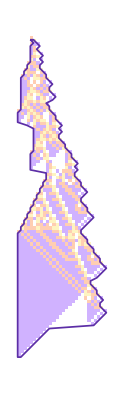
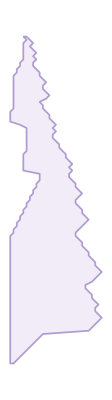
-Graphics--Graphics--Graphics-

## Examples

### Basic Examples

Run a cellular automaton with a random perturbation for 2 steps, here the first cell of the second row is flipped to 0:

```mathematica
PerturbedCellularAutomaton[30,{{1},0},{2, {-2, 2}}]
```

{{{0,0,1,0,0},{0,1,1,1,0},{0,1,0,0,1}},<|{2,1}→0|>}

Specify that same perturbation:

```mathematica
PerturbedCellularAutomaton[30,{{1},0},{2, {-2, 2}}, {2, 1}->0]
```

{{{0,0,1,0,0},{0,1,1,1,0},{0,1,0,0,1}},<|{2,1}→0|>}

### Scope

See the differences based on the perturbation above:

```mathematica
ArrayPlot/@ {CellularAutomaton[30,{{1},0},{2, {-2, 2}}], First[PerturbedCellularAutomaton[30,{{1},0},{2, {-2, 2}}, {2, 1}->0]]}
```

{-Graphics-,-Graphics-}

Draw an arrow to the perturbed cell:

```mathematica
Module[{ca = First[#], pert = Last[#]},ArrayPlot[ca,Epilog->{Arrowheads[Large],Style[Arrow[{{0, Length[ca] - #1 -.5},{#2-.5 ,Length[ca] - #1 -.5}}], Red]&@@@Keys[pert]}]]&[ PerturbedCellularAutomaton[30,{{1},0},{2, {-2, 2}}, {2, 1}->0]]
```

-Graphics-

Do two random perturbations:

```mathematica
data=PerturbedCellularAutomaton[30,{{1},0},{2, {-2, 2}},2]
```

{{{0,0,1,0,0},{0,0,1,1,0},{0,1,0,0,1}},<|{1,2}→0,{2,3}→0|>}

Visualize it:

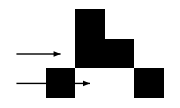

```mathematica
Module[{ca = First[#], pert = Last[#]},ArrayPlot[ca,Epilog->{Arrowheads[Large],Style[Arrow[{{0, Length[ca] - #1 -.5},{#2-.5 ,Length[ca] - #1 -.5}}], Red]&@@@Keys[pert]}]]&[ data]
```

Use those same perturbation locations but set them both to white:

```mathematica
Module[{ca = First[#], pert = Last[#]},ArrayPlot[ca,Epilog->{Arrowheads[Large],Style[Arrow[{{0, Length[ca] - #1 -.5},{#2-.5 ,Length[ca] - #1 -.5}}], Red]&@@@Keys[pert]}]]&[ PerturbedCellularAutomaton[30,{{1},0},{2, {-2, 2}}, {{1, 2}, {2, 4}}->0]]
```

-Graphics-

Do a range of three perturbations at timestep two:

```mathematica
data=PerturbedCellularAutomaton[30,{{1},0},{2, {-2, 2}}, {2,2;;4}]
```

{{{0,0,1,0,0},{0,1,1,1,0},{1,0,1,1,1}},<|{2,2}→0,{2,3}→1,{2,4}→1|>}

Visualize it:

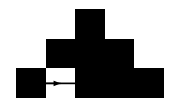

```mathematica
Module[{ca = First[#], pert = Last[#]},ArrayPlot[ca,Epilog->{Arrowheads[Large],Style[Arrow[{{0, Length[ca] - #1 -.5},{#2-.5 ,Length[ca] - #1 -.5}}], Red]&@@@Keys[pert]}]]&[ data]
```

Perturb the third cell at timestep one and two:

```mathematica
data=PerturbedCellularAutomaton[30,{{1},0},{2, {-2, 2}}, {1;;2,3}]
```

{{{0,0,1,0,0},{0,1,0,1,0},{1,1,1,1,1}},<|{1,3}→0,{2,3}→1|>}

Visualize it:

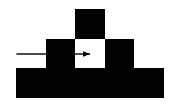

```mathematica
Module[{ca = First[#], pert = Last[#]},ArrayPlot[ca,Epilog->{Arrowheads[Large],Style[Arrow[{{0, Length[ca] - #1 -.5},{#2-.5 ,Length[ca] - #1 -.5}}], Red]&@@@Keys[pert]}]]&[ data]
```

Perturb a random sample of three at the second timestep:

```mathematica
data=PerturbedCellularAutomaton[30,{{1},0},{2, {-2, 2}}, {2,RandomSample[#, 3]&}]
```

{{{0,0,1,0,0},{0,1,1,1,0},{1,0,1,1,1}},<|{2,3}→1,{2,2}→0,{2,4}→1|>}

Visualize it:

```mathematica
Module[{ca = First[#], pert = Last[#]},ArrayPlot[ca,Epilog->{Arrowheads[Large],Style[Arrow[{{0, Length[ca] - #1 -.5},{#2-.5 ,Length[ca] - #1 -.5}}], Red]&@@@Keys[pert]}]]&[ data]
```

-Graphics-

Perturb the last cell at every timestep:

```mathematica
Module[{ca = First[#], pert = Last[#]},ArrayPlot[ca,Epilog->{Arrowheads[Large],Style[Arrow[{{0, Length[ca] - #1 -.5},{#2-.5 ,Length[ca] - #1 -.5}}], Red]&@@@Keys[pert]}]]&[ PerturbedCellularAutomaton[30,{{1},0},{2, {-2, 2}}, {;;All,Last}]]
```

-Graphics-

With larger k-values, you can use "AddValue" for the bit specification to make a deterministic change. Here yellow always gets flipped to white:

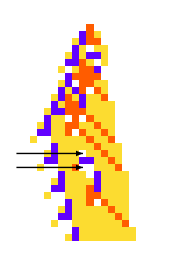

```mathematica
Module[{ca = First[#], pert = Last[#]},ArrayPlot[ca, ColorRules-> {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},Epilog->{Arrowheads[Large],Arrow[{{0, Length[ca] - #1 -.5},{#2-.5 ,Length[ca] - #1 -.5}}]&@@@Keys[pert]}]]&[PerturbedCellularAutomaton[{297413946807002990892857386679107573048,4,1}, {{1}, 0}, {30, {-10, 10}}, {{20, 10}, {18, 10}}->{"AddValue", 1}]]
```

### Options

Setting "ReturnPerturbations" to False makes it so that only evolution of the automata is returned:

```mathematica
PerturbedCellularAutomaton[30,{{1},0},{2, {-2, 2}}, "ReturnPerturbations"->False]
```

{{0,0,1,0,0},{0,1,1,0,0},{1,1,0,1,0}}

Setting "Body" to true makes it so that the specified index is interpreted as the index within the non-zero range of the automata:

```mathematica
Module[{ca = First[#], pert = Last[#]},ArrayPlot[ca,Epilog->{Arrowheads[Large],Style[Arrow[{{0, Length[ca] - #1 -.5},{#2-.5 ,Length[ca] - #1 -.5}}], Red]&@@@Keys[pert]}]]&[ PerturbedCellularAutomaton[30,{{1},0},{2, {-2, 2}}, {1, 1}->0, "Body"->True]]
```

-Graphics-

### Applications

Evolve a rule with perturbations:

```mathematica
robustru = Module[{ru, ca, lt, pcas, fitness, testcalifetime = Function[ca, If[#==0, -Infinity, Length[ca]-#]&[LengthWhile[Reverse[ca],Total[#]==0&]]]},
SeedRandom[511114];
Nest[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
ca = CellularAutomaton[ru,{{1}, 0}, {200, {-50, 50}}];
lt = testcalifetime[ca];
If[lt == -Infinity, #,
pcas = Table[PerturbedCellularAutomaton[ru, {{1}, 0}, {200, {-50, 50}}, "ReturnPerturbations"->False], Ceiling[lt/20]];
fitness = Min[Join[{lt}, testcalifetime/@ pcas]];
If[fitness>=Last[#],{ru,fitness},#]
]]&,{{0,4,1},0},1000]
] // First;
```

Plotting our robust automaton:

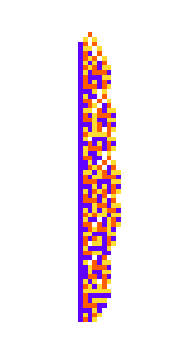

```mathematica
ArrayPlot[CellularAutomaton[robustru, {{1}, 0}, {60, {-15, 15}}], ColorRules-> {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]
```

Ten sample perturbations:

```mathematica
Module[{ca = First[#], pert = Last[#]},ArrayPlot[ca,ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},Epilog->{Arrowheads[Large],Arrow[{{0, Length[ca] - #1 -.5},{#2-.5 ,Length[ca] - #1 -.5}}]&@@@Keys[pert]}]]&/@ Table[PerturbedCellularAutomaton[robustru, {{1}, 0}, {200, {-20, 20}}], 10]
```

-Graphics-

Plot the lifetime distribution of one thousand different random single perturbations:

```mathematica
lts = Function[ca, If[#==0, 202, Length[ca]-#]&[LengthWhile[Reverse[ca],Total[#]==0&]]]/@ Table[PerturbedCellularAutomaton[robustru, {{1}, 0}, {200, {-20, 20}}, "ReturnPerturbations"->False], 1000];
Histogram[lts, PlotRange->All]
```

-Graphics-

Obtain the mortality curve:

```mathematica
Histogram[lts, {10}, "CDF"]
```

-Graphics-

### Possible Issues

When you specify an index outside the range of the body, an empty perturbation is returned:

```mathematica
PerturbedCellularAutomaton[30,{{1},0},{2, {-2, 2}}, {1, 4}, "Body"->True]
```

{{{0,0,1,0,0},{0,1,1,1,0},{1,1,0,0,1}},<||>}

The tspec uses the same indexing as in CellularAutomaton, so the initial row is perturbed using zero:

```mathematica
PerturbedCellularAutomaton[30,{{1},0},{2, {-2, 2}},{0, 1}]
```

{{{1,0,1,0,0},{1,0,1,1,1},{0,0,1,0,0}},<|{0,1}→1|>}

Because the automata are stitched together, using All or Automatic as an xspec is not allowed. If no xspec is given, or All or Automatic are given, xspec defaults to {-25,25}:

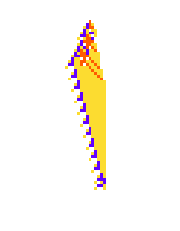

```mathematica
ArrayPlot[First[PerturbedCellularAutomaton[{297413946807002990892857386679107573048,4,1}, {{1}, 0}, 65]], ColorRules-> {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]
```

Doing many perturbations sometimes results in the body dying out, with no perturbations left to perform:

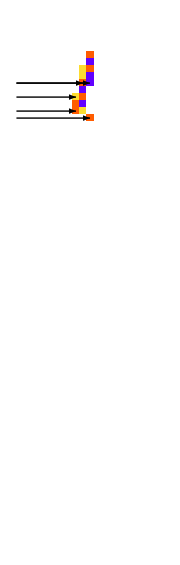

```mathematica
Module[{ca = First[#], pert = Last[#]},ArrayPlot[ca, ColorRules-> {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},Epilog->{Arrowheads[Large],Arrow[{{0, Length[ca] - #1 +.5},{#2-.5 ,Length[ca] - #1 +.5}}]&@@@Keys[pert]}]]&[PerturbedCellularAutomaton[{180311482541120044137557119353943331376,4,1}, {{1}, 0}, {65, {-10, 10}}, 10]]
```

Running the function on an empty list or association returns the unperturbed cellular automaton:

```mathematica
PerturbedCellularAutomaton[30,{{1},0},{2, {-2, 2}}, <||>]
```

{{0,0,1,0,0},{0,1,1,1,0},{1,1,0,0,1}}

### Neat Examples

Rules that "age" are particularly robust to perturbations:

```mathematica
Module[{ca = First[#], pert = Last[#]},ArrayPlot[ca, ColorRules-> {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},Epilog->{Arrowheads[Large],Arrow[{{0, Length[ca] - #1 +.5},{#2-.5 ,Length[ca] - #1 +.5}}]&@@@Keys[pert]}]]&[PerturbedCellularAutomaton[{297413946807002990892857386679107573048,4,1}, {{1}, 0}, {65, {-10, 10}}]]
```

-Graphics-

They can also be healed easily. Here we apply a therapeutic perturbation:

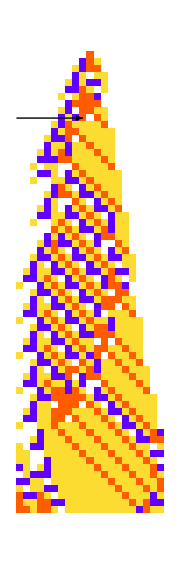
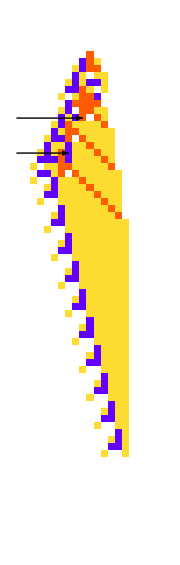

```mathematica
Module[{ca = First[#], pert = Last[#]},ArrayPlot[ca, ColorRules-> {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},Epilog->{Arrowheads[Large],Arrow[{{0, Length[ca] - #1 +.5},{#2-.5 ,Length[ca] - #1 +.5}}]&@@@Keys[pert]}]]&/@(PerturbedCellularAutomaton[{297413946807002990892857386679107573048,4,1}, {{1}, 0}, {65, {-10, 10}},#]& /@ {{10, 10}->3,{{10, 10}->3,{15, 8}->2}})
```

With random perturbations you can see the beginning of self-reproduction in very simple rules:

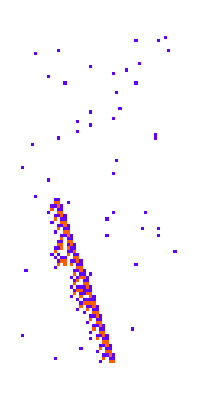

```mathematica
coords = Transpose@{RandomInteger[{1, 1000}, 500], RandomInteger[{1, 50}, 500]}->2;
ArrayPlot[#, ColorRules-> {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]&[PerturbedCellularAutomaton[{3019941697641,3,1}, {{1}, 0}, {{900, 1000}, {-25, 25}}, coords, "ReturnPerturbations"->False]]
```

## Source & Additional Information

### Contributed By

Willem Nielsen, Stephen Wolfram and Dugan Hammock

### Keywords

CellularAutomata

Medicine

Therapy

Disease

Biology

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

CellularAutomaton

### Related Resource Objects

RandomCA

MultiwayAggregationSystem

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.